```mathematica
H={
{1,0},
{Cos[30 °],Sin[30°]},
{Cos[-45 °],Sin[-45°]},
{Cos[-30 °],Sin[-30°]},
{Cos[-30 °],Sin[-30°]},
{Cos[30 °],Sin[30°]},
{Cos[30 °],Sin[30°]}}//N;
weight={0,1,0,1,0,0,1};
wH = weight H;
CoVar =Inverse[Transpose[wH].wH] ;
G = CoVar.Transpose[wH];
MatrixForm[wH]
MatrixForm[G]
MatrixForm[CoVar]
```

(0. | 0.
0.866025 | 0.5
0. | 0.
0.866025 | -0.5
0. | 0.
0. | 0.
0.866025 | 0.5)

(0. | 0.288675 | 0. | 0.57735 | 0. | 0. | 0.288675
0. | 0.5 | 0. | -1. | 0. | 0. | 0.5)

(0.5 | -0.288675
-0.288675 | 1.5)

```mathematica
tempPos={0, -1.02,0,7.99,0,0,2.07};
tempPara=G.tempPos
Predict=H.tempPara;
Residual=tempPos-weight Predict;
SSR = Norm[Residual]^2
TableForm[{tempPos,Predict,Residual}]
MatrixForm[CoVar SSR]
{√(CoVar[[1,1]]SSR),√(CoVar[[2,2]]SSR)}
LinearModelFit[{wH,tempPos},{x,y}][{"BestFitParameters","ANOVATable","CovarianceMatrix","FitResiduals","ParameterTable","ParameterConfidenceIntervalTable"}]
```

{4.91614,-7.465}

4.77405

0 | -1.02 | 0 | 7.99 | 0 | 0 | 2.07
4.91614 | 0.525 | 8.75479 | 7.99 | 7.99 | 0.525 | 0.525
0. | -1.545 | 0. | 0. | 0. | 0. | 1.545

(2.38703 | -1.37815
-1.37815 | 7.16107)

{1.545,2.67602}

{{4.91614,-7.465}, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 27.2405 | 27.2405 | 28.5298 | 0.00308592
y | 1 | 37.1508 | 37.1508 | 38.9091 | 0.00155042
Error | 5 | 4.77405 | 0.95481 |  | 
Total | 7 | 69.1654 |  |  | ,{{0.477405,-0.27563},{-0.27563,1.43221}},{0.,-1.545,0.,-1.77636×10^-15,0.,0.,1.545}, | Estimate | Standard Error | t-Statistic | P-Value
x | 4.91614 | 0.690945 | 7.11509 | 0.000850384
y | -7.465 | 1.19675 | -6.23772 | 0.00155042, | Estimate | Standard Error | Confidence Interval
x | 4.91614 | 0.690945 | {3.14001,6.69227}
y | -7.465 | 1.19675 | {-10.5413,-4.38865}}

## Trimmed Matrix

```mathematica
wH
weight
Delete[wH,Position[weight,0]]
```

{{0.,0.},{0.866025,0.5},{0.,0.},{0.866025,-0.5},{0.,0.},{0.,0.},{0.866025,0.5}}

{0,1,0,1,0,0,1}

{{0.866025,0.5},{0.866025,-0.5},{0.866025,0.5}}

```mathematica
tH = Delete[wH,Position[weight,0]];
CoVartH=Inverse[Transpose[tH].tH];
tG = CoVartH.Transpose[tH];
MatrixForm[tH]
MatrixForm[tG]
MatrixForm[CoVartH]
```

(0.866025 | 0.5
0.866025 | -0.5
0.866025 | 0.5)

(0.288675 | 0.57735 | 0.288675
0.5 | -1. | 0.5)

(0.5 | -0.288675
-0.288675 | 1.5)

```mathematica
tempPost=Delete[{0, -1.02,0,7.99,0,0,2.07},Position[weight,0]];
tempParat=tG.tempPost
Predictt=tH.tempParat;
Residualt=tempPost-Predictt;
SSRt = Norm[Residualt]^2
TableForm[{tempPost,Predictt,Residualt}]
MatrixForm[CoVartH SSRt]
{√(CoVartH[[1,1]]SSRt),√(CoVartH[[2,2]]SSRt)}
LinearModelFit[{tH,tempPost},{x,y}][{"BestFitParameters","ANOVATable","CovarianceMatrix","FitResiduals","ParameterTable","ParameterConfidenceIntervalTable"}]
```

{4.91614,-7.465}

4.77405

-1.02 | 7.99 | 2.07
0.525 | 7.99 | 0.525
-1.545 | 0. | 1.545

(2.38703 | -1.37815
-1.37815 | 7.16107)

{1.545,2.67602}

{{4.91614,-7.465}, | DF | SS | MS | F-Statistic | P-Value
y | 1 | 37.1508 | 37.1508 | 7.78182 | 0.219128
Error | 1 | 4.77405 | 4.77405 |  | 
Total | 2 | 41.9249 |  |  | ,{{2.38702,-1.37815},{-1.37815,7.16108}},{-1.545,-1.77636×10^-15,1.545}, | Estimate | Standard Error | t-Statistic | P-Value
x | 4.91614 | 1.545 | 3.18197 | 0.193849
y | -7.465 | 2.67602 | -2.78959 | 0.219128, | Estimate | Standard Error | Confidence Interval
x | 4.91614 | 1.545 | {-14.7149,24.5472}
y | -7.465 | 2.67602 | {-41.467,26.537}}

## Comaparison

```mathematica
LinearModelFit[{wH,tempPos},{x,y}][{"BestFitParameters","ANOVATable","CovarianceMatrix","FitResiduals","ParameterTable","ParameterConfidenceIntervalTable"}]
LinearModelFit[{tH,tempPost},{x,y}][{"BestFitParameters","ANOVATable","CovarianceMatrix","FitResiduals","ParameterTable","ParameterConfidenceIntervalTable"}]
```

{{4.91614,-7.465}, | DF | SS | MS | F-Statistic | P-Value
x | 1 | 27.2405 | 27.2405 | 28.5298 | 0.00308592
y | 1 | 37.1508 | 37.1508 | 38.9091 | 0.00155042
Error | 5 | 4.77405 | 0.95481 |  | 
Total | 7 | 69.1654 |  |  | ,{{0.477405,-0.27563},{-0.27563,1.43221}},{0.,-1.545,0.,-1.77636×10^-15,0.,0.,1.545}, | Estimate | Standard Error | t-Statistic | P-Value
x | 4.91614 | 0.690945 | 7.11509 | 0.000850384
y | -7.465 | 1.19675 | -6.23772 | 0.00155042, | Estimate | Standard Error | Confidence Interval
x | 4.91614 | 0.690945 | {3.14001,6.69227}
y | -7.465 | 1.19675 | {-10.5413,-4.38865}}

{{4.91614,-7.465}, | DF | SS | MS | F-Statistic | P-Value
y | 1 | 37.1508 | 37.1508 | 7.78182 | 0.219128
Error | 1 | 4.77405 | 4.77405 |  | 
Total | 2 | 41.9249 |  |  | ,{{2.38702,-1.37815},{-1.37815,7.16108}},{-1.545,-1.77636×10^-15,1.545}, | Estimate | Standard Error | t-Statistic | P-Value
x | 4.91614 | 1.545 | 3.18197 | 0.193849
y | -7.465 | 2.67602 | -2.78959 | 0.219128, | Estimate | Standard Error | Confidence Interval
x | 4.91614 | 1.545 | {-14.7149,24.5472}
y | -7.465 | 2.67602 | {-41.467,26.537}}

```mathematica
(* because the DF of error is 5 times more, the Standard error is 5 time smaller *)
```

```mathematica
Needs["HypothesisTesting`"]
```

```mathematica
StudentTCI[4.9161375,1.545,1,ConfidenceLevel->.95]
```

{-14.7149,24.5472}

```mathematica
InverseCDF[StudentTDistribution[4.9161375, 1.545,1],0.975]
InverseCDF[StudentTDistribution[4.9161375, 1.545,1],0.025]
```

24.5472

-14.7149

```mathematica
InverseCDF[StudentTDistribution[1],0.025] 1.545 + 4.9161375
```

-14.7149

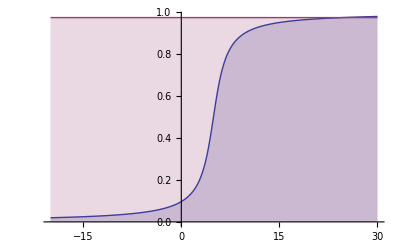

```mathematica
Plot[{
Evaluate@CDF[StudentTDistribution[4.9161375,1.545,1],x],0.975
},{x,-20,30},Filling->Axis]
```

```mathematica
CDF[StudentTDistribution[1],0.975]
```

0.745971

```mathematica
PDF[StudentTDistribution[1],0]//N
```

0.31831

```mathematica
InverseCDF[StudentTDistribution[1],0.975]
```

12.7062